# Inclined Fusion Pore Energy

Curtis Sera
v1.1.0, 2020-02-14

## Set - up : Establishing the Coordinate System

Let’s try applying the inclined membrane pore solution from Christoph & Rob’s paper.
Adapting it to a bent membrane rather than a bent monolayer, it has the following coordinate scheme:
-Graphics-

First let’s just check that we can get their results in Mathematica to begin with

## Test Application to Published Monolayer Pore Situation

Let' s try to replicate fig 5 from Christoph and Rob' s paper just to verify that things are working

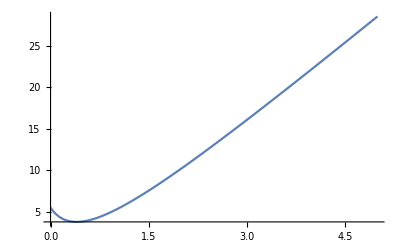

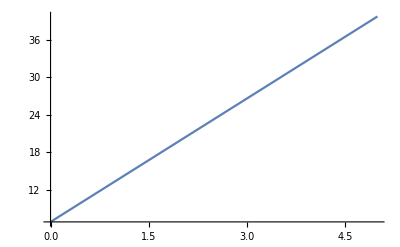

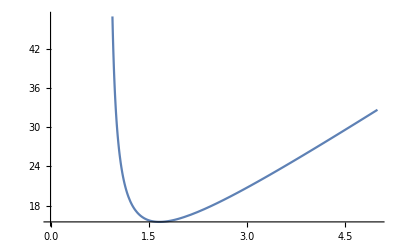

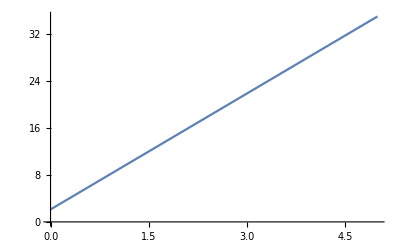

```mathematica
Kb=1; (* kT; Helfrich bending constant *)
H0=0; (* 1/nm; spontaneous curvature *)
h=0.5; (* nm; membrane thickness *)
R1=1.5; (* nm; assume that the membranes are within the critical distance for hemifusion *)
m=h+R1;
R2[r_,ω_,a_]:=R1 - ((r+m Cos[a])/(Cos[PlusMinus[Abs[ω],a]]));

ξ[r_,a_]:=(r+m Cos[a])/(R1);
W[r_,a_]:=(2ξ[r,a]^2)/(Sqrt[ξ[r,a]^(2)-1]) * (ArcTan[(Sqrt[ξ[r,a]^(2)-1]* Tan[(a/2)+(Pi/4)])/(ξ[r,a]-1)]-ArcTan[(Sqrt[ξ[r,a]^(2)-1]*Tan[a/2])/(ξ[r,a]-1)]);
T[r_,a_]:=-4 Cos[a]-H0 R1 (Pi ξ[r,a] - 4 Cos[a])+H0^2 R1^2 ((ξ[r,a] Pi)/2 - Cos[a]);

G[r_,a_]:=Pi Kb (W[r,a]+W[r,-a]+2 T[r,a]);
GRim[r_,a_]:=Pi Kb (Pi ξ[r,a]-2 Cos[a]);

Plot[G[r,0],{r,0,5}]
Plot[GRim[r,0],{r,0,5}]
Plot[G[r,0.4 Pi],{r,0,5}]
Plot[GRim[r,0.4Pi],{r,0,5}]
```

```mathematica
G[0,0]
G[0.5,0]
G[1,0]
G[5,0]
G[0.5, 0.4 Pi]
G[0,Pi/4]
W[0.5,0.4 Pi]
T[0.5,0.4 Pi]
```

5.50382

3.85234

5.25776

28.5036

-10.3938+8.22467 ⅈ

-26.3481+52.6379 ⅈ

0.87276+0. ⅈ

-1.23607

This appears to be happening because the range for ξ is being broken.  Their solution requires ξ > 1, but I’m feeding it conditions where ξ < 1 which is making G complex.  Specifically, the source of the complex component appears to be the W function due to the sqrt[ξ^2 - 1] bits.  This makes sense but is quite confusing given that I’m using the exact conditions they supposedly feed to the solution in fig 5 of their paper...

## Stress of published inclined pore

So I don' t know what' s up with the G for θ < 2 nm, but I’ll go ahead and give the pore E per unit length with what I have for now

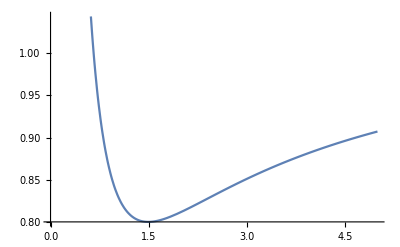

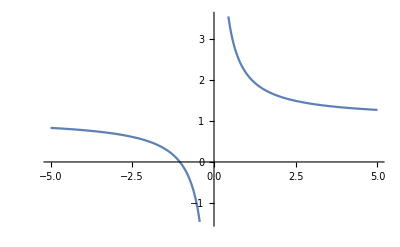

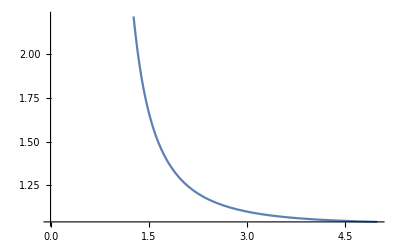

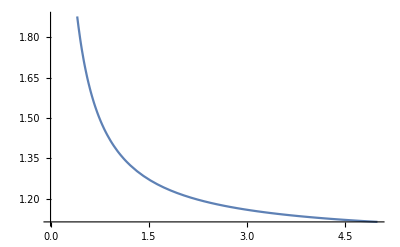

```mathematica
GLength[r_,a_]:=G[r,a]/(2*Pi*r);
GRimLength[r_,a_]:=Grim[r,a]/(2*Pi*r);

Plot[GLength[r,0],{r,0,5}]
Plot[GRimLength[r,0],{r,0,5}]
Plot[GLength[r,0.4 Pi],{r,0,5}]
Plot[GRimLength[r,0.4Pi],{r,0,5}]
```

Fascinating what happens with the total pore pseudo-stress.  This indicates...?  Unlike total pore E for θ = 0 which reaches a minimum at r = ~0.5 nm, the pseudo-stress reaches a minimum at r = ~1.5 nm.  Meanwhile, the rim contribution has gone from linear (G = a r + b) increase to rational (G/r = a + b/r) decay.

## Inclined fusion pore

Ok, well I' m still not sure why I' m getting something different than in fig 5, but I' ll try applying it to a hypothetical fusion pore anyway while I wait for Christoph to give feedback.
First, I’ll read in the relevant parameters based on Aeffner et al’s x-ray diffraction (2012) measurements.  They found that at the hemifusion stalk stage, the hemifused monolayers were separated by ~2 nm (compare to Yang and Huang, 2002 who observed d = 1 nm), the bilayers were ~3 nm thick, and the hemifusion stalk had a minimum diameter of ~2 nm.  So...

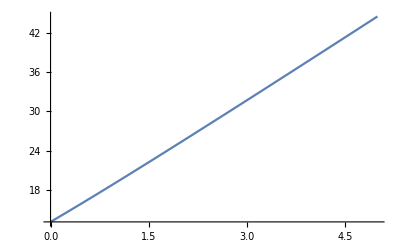

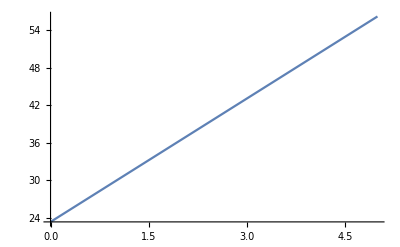

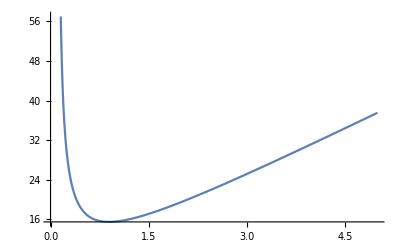

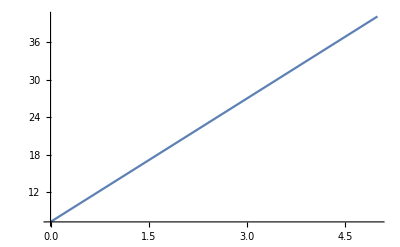

```mathematica
R1Meas=1.5; (* nm; assume that the membranes are within the critical distance for hemifusion *)
hMeas = 3; (* nm; Measured membrane thickness *)

Kb=1; (* kT; Helfrich bending constant *)
H0=0; (* 1/nm; spontaneous curvature *)
m=hMeas+R1Meas;

R2[r_,ω_,a_]:=R1Meas - ((r+m Cos[a])/(Cos[PlusMinus[Abs[ω],a]]));

ξMeas[r_,a_]:=(r+m Cos[a])/(R1Meas);
WMeas[r_,a_]:=(2ξMeas[r,a]^2)/(Sqrt[ξMeas[r,a]^(2)-1]) * (ArcTan[(Sqrt[ξMeas[r,a]^(2)-1]* Tan[(a/2)+(Pi/4)])/(ξMeas[r,a]-1)]-ArcTan[(Sqrt[ξMeas[r,a]^(2)-1]*Tan[a/2])/(ξMeas[r,a]-1)]);
TMeas[r_,a_]:=-4 Cos[a]-H0 R1Meas (Pi ξ[r,a] - 4 Cos[a])+H0^2 R1Meas^2 ((ξMeas[r,a] Pi)/2 - Cos[a]);

GMeas[r_,a_]:=Pi Kb (WMeas[r,a]+WMeas[r,-a]+2 TMeas[r,a]);
GRimMeas[r_,a_]:=Pi Kb (Pi ξMeas[r,a]-2 Cos[a]);

Plot[GMeas[r,0],{r,0,5}]
Plot[GRimMeas[r,0],{r,0,5}]
Plot[GMeas[r,0.4 Pi],{r,0,5}]
Plot[GRimMeas[r,0.4Pi],{r,0,5}]
```